# Sensitivity of IVP solutions

## First order system

We want to asses the sensitivity of solutions of the 1st order system
	u'=f(u) with  u(0)=x
to the initial condition u(0)=x.  Note u is a vector valued function of time t.  All we need to do is differentiate the equation with respect to x.  We get the matrix valued IVP
	(∂_x u)'=Df(u).∂_x u  with ∂_x u(0)=I
which looks a bit less exotic 
	J'=Df(u).J  with J(0)=I
if we write J(t)=∂_x u(t) for the matrix valued function.

### Example

```mathematica
Clear[f]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z, x+ a y, b+ z (x-c)}
Df[{a_,b_,c_}][{x_,y_,z_}]:={{0,-1,-1},{1,a,0},{z,0,-c+x}}
TMax=45;u0={1,2,3};{a,b,c}={0.2,0.2,5.7};
{uSol,JSol}=NDSolveValue[{
u'[t]==f[{a,b,c}][u[t]],
 J'[t]==Df[{a,b,c}][u[t]].J[t],
u[0]==u0,J[0]==IdentityMatrix[3]},
{u,J},{t,0, TMax}];
ParametricPlot3D[uSol[t],{t,0, TMax},PlotRange->All]
```

-Graphics3D-

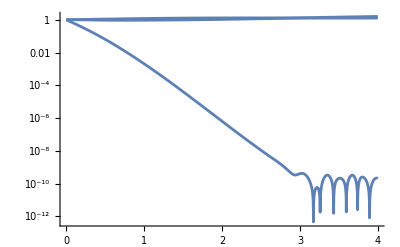

```mathematica
LogPlot[ SingularValueList[JSol[t]],{t, 0, 4}]
```